```mathematica
SetDirectory["L:/moose/project2/trunk/elk"]
```

L:\moose\project2\trunk\elk

```mathematica
ClearAll[f,u,uprime,zstar,theta,tau,z];
kn=0;
ks = 1;
deltaK=ks-kn;
thn=0;
ths=1;
deltatheta=ths-thn;
cc = 1.5;
las=2;
rr=0.5;
rrstar=(rr-kn)/deltaK;
m=4cc(cc-1);
rho=rrstar/m;
ts=las*deltatheta/deltaK;

f[x_] := Exp[x^2]Erfc[x];

u[zeta_,tau_]:=(1/2)Exp[-zeta^2/tau](2Exp[((zeta+rho*tau)/Sqrt[tau])^2] + f[(zeta-rho*Sqrt[1+1/rho]*tau)/Sqrt[tau]]-f[(zeta-rho tau)/Sqrt[tau]] + f[(zeta+rho*Sqrt[1+1/rho]*tau)/Sqrt[tau]]-f[(zeta+rho tau)/Sqrt[tau]]);
uprime[zeta_,tau_]:=Evaluate[D[u[z,tau],z]/.z->zeta];

zstar[zeta_,tau_]:=(1/cc)*(rho^2 (1+1/rho) tau + rho (2+1/rho) zeta - Log[u[zeta,tau]]);
theta[zeta_,tau_]:=cc*(1 - 1/(2rho+1-uprime[zeta,tau]/u[zeta,tau]));

tau[t_] := m*t/ts;
z[zeta_,tau_] := las*zstar[zeta,tau];
```

```mathematica
ans={theta[#,tau[8]],z[#,tau[8]]}&/@Range[0,7,0.01];
```

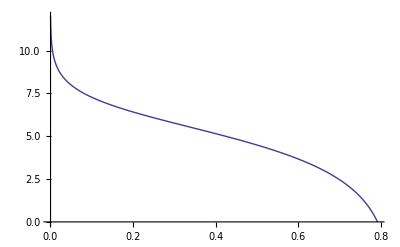

```mathematica
ListLinePlot[ans,PlotRange->All]
```

```mathematica
Export["doc/richards/tests/data/bw01_analytic_8.csv",ans,"Table"]
```

doc/richards/tests/data/bw01_analytic_8.csv